20000

1

1

(4 √2)/3

√2

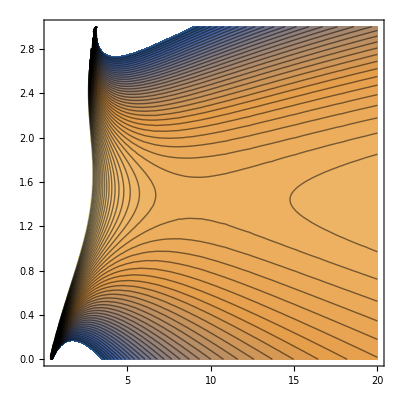

-Graphics3D-

-(20000 T)/(x (x-y))-(20000 (2 y-y^3/3))/x^2+(20000 T (1+Log[x-y]))/x^2

(20000 T)/(x (x-y))+(20000 (2-y^2))/x

{{x→9.36208,y→1.45826}}

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{1,2,3,4,5,6,7,8,9,10}

{1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45}

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{{},{},{},{},{},{},{},{{x→68.8573,y→1.41657}},{{x→46.2459,y→1.41815}},{{x→33.6339,y→1.42024}},{{x→25.9674,y→1.42283}},{{x→20.9871,y→1.42591}},{{x→17.5774,y→1.42946}},{{x→15.142,y→1.43343}},{{x→13.3412,y→1.43778}},{{x→11.9706,y→1.44248}},{{x→10.9019,y→1.44748}},{{x→10.0512,y→1.45275}},{{x→9.36208,y→1.45826}}}

{{x,y},{x,y},{x,y},{x,y},{x,y},{x,y},{x,y},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{x→1.54574×10^8,y→1.41421},{x→288023.,y→1.41421},{x→12435.6,y→1.41422},{x→1889.32,y→1.41426},{x→539.502,y→1.41441},{x→221.476,y→1.41478},{x→114.324,y→1.41547},{x→68.8573,y→1.41657},{x→46.2459,y→1.41815},{x→33.6339,y→1.42024},{x→25.9674,y→1.42283},{x→20.9871,y→1.42591},{x→17.5774,y→1.42946},{x→15.142,y→1.43343},{x→13.3412,y→1.43778},{x→11.9706,y→1.44248},{x→10.9019,y→1.44748},{x→10.0512,y→1.45275},{x→9.36208,y→1.45826}}

{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}

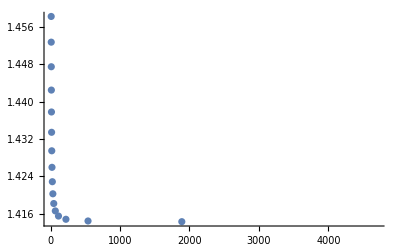

```mathematica
L = 20000
gamma = 1
sigma = 1
Clear[T]

(* T = 1, 1 = 3*)


saddleenergy= (4/3)*(√2/sigma)
crackcrit = √2/sigma


F1[x_,y_, T_] := -T*(L/x)* (Log[L/(L/x)- y]+1) +  (L/x)*((-y^3/3)*sigma^2 +2*y*gamma)


ContourPlot[F1[x,y,1],{x,0.4,20},{y,0,3}, Contours->50]
Plot3D[F1[x,y, 1] ,{x,0.4,10},{y,0,3},RegionFunction->Function[{x,y},x > y],ColorFunction->(ColorData["DarkRainbow"][#3]&),PlotRange->Automatic]

F1partx[x_,T_]=D[F1[x,y,T],x]
F1party[y_,T_]=D[F1[x,y,T],y]


s = NSolve[F1partx[x,1]==0&& F1party [y, 1]==0 && 3 < x< 70&& 1< y<20,{x,y}]

T = Range[0.1,1,0.05]

T=Range[10] (*a={1,2,3,4,5,6,7,8,9,10}*) 
T = Range[1,1.45,0.05]
T = Range[0.1,1,0.05]
T

list=Table[NSolve[F1partx[x,T[[i]]]==0&&F1party[y,T[[i]]]==0 && 3 < x< 70&& 1< y<20,{x,y}],{i,1,19}]
{x,y}/.Flatten/@list

list1=Table[FindRoot[{F1partx[x,T[[i]]]==0,F1party[y,T[[i]]]==0},{{x,Exp[saddleenergy/T[[i]]]},{y,Sqrt[2]}}],{i,1,19}]

fava={x,y}/.Flatten/@list1

ListPlot[fava ]
```

```mathematica
a
```

a

```mathematica
fava
```

{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}

```mathematica
a=2^(1/2)
```

√2

```mathematica
√2
a
```

√2

√2

```mathematica
F1[4,2,1]
```

20000/3-5000 (1+Log[2])

```mathematica
F1[fava,1]
```

F1[{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}},1]

```mathematica
F1[fava,2]
```

F1[{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}},2]

```mathematica
fava
```

{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}

```mathematica
fava[1]
```

{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}[1]

```mathematica
G[Temp_]:= 3*Exp[-1/Temp]
```

```mathematica
Series[G[Temp],{Temp,0,10}]
```

3 ⅇ^(-1/Temp+O[Temp]^11)

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
mtrixform[fava ]
```

mtrixform[{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}]

```mathematica
MatrixForm[fava]
```

(1.54574×10^8 | 1.41421
288023. | 1.41421
12435.6 | 1.41422
1889.32 | 1.41426
539.502 | 1.41441
221.476 | 1.41478
114.324 | 1.41547
68.8573 | 1.41657
46.2459 | 1.41815
33.6339 | 1.42024
25.9674 | 1.42283
20.9871 | 1.42591
17.5774 | 1.42946
15.142 | 1.43343
13.3412 | 1.43778
11.9706 | 1.44248
10.9019 | 1.44748
10.0512 | 1.45275
9.36208 | 1.45826)

```mathematica
Fmeta[ccrit_ , T_]:= L*Exp[-(   (-ccrit^3/3)*sigma^2 +2*ccrit*gamma)/T] * (-T*(Log[Exp[(   (-ccrit^3/3)*sigma^2 +2*ccrit*gamma)/T]-ccrit]+1) + (-ccrit^3/3)*sigma^2 +2*ccrit*gamma)
Fmeta[0.01,0.001]
```

-4.12368×10^-8

```mathematica
Fmetalow[ccrit_, T_]:= L*Exp[-(   (-ccrit^3/3)*sigma^2 +2*ccrit*gamma)/T]*(-T)
```

```mathematica
Fmetalow[0.03, 2]
```

-38818.

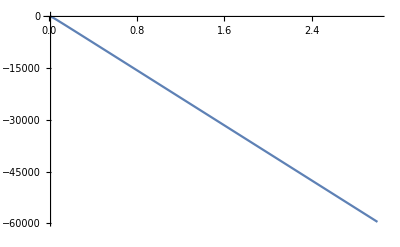

```mathematica
Plot[Fmetalow[0.01, T],{T,0.01,3}]
```

```mathematica
Plot[{Fmeta[0.1, T],Fmetalow[0.1, T]},{T, 0.001, 1},PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
crackcrit
```

√2

```mathematica
Fsaddle[ T_] := -T*(L*Exp[-saddleenergy/T])* ((Log[Exp[saddleenergy/T]- crackcrit]+1) + saddleenergy)  

Fsaddle[1]
```

-20000 ⅇ^(-(4 √2)/3) (1+(4 √2)/3+Log[-√2+ⅇ^((4 √2)/3)])

```mathematica
-3 ⅇ^(-(4 √2)/3) (1+(4 √2)/3+Log[-√2+ⅇ^((4 √2)/3)])

Log[-√2+ⅇ^((4 √2)/3)]
```

-3 ⅇ^(-(4 √2)/3) (1+(4 √2)/3+Log[-√2+ⅇ^((4 √2)/3)])

Log[-√2+ⅇ^((4 √2)/3)]

```mathematica
Exp[4*√2/3]
```

ⅇ^((4 √2)/3)

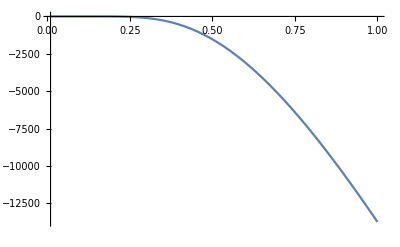

```mathematica
perturbsaddle=Plot[Fsaddle[T],{T,0.01,1}]
```

```mathematica
Series[Fsaddle[x],{x,0,10}]
```

ⅇ^(-(4 √2)/(3 x)+O[x]^11) (Log[-√2+ⅇ^((4 √2)/(3 x)+O[x]^11)] (-20000 x+O[x]^11)+((-20000-(80000 √2)/3) x+O[x]^11))

```mathematica
Series[Fmetalow[ccrit, x],{x,0,10}]
```

ⅇ^((-2 ccrit+ccrit^3/3)/x+O[x]^11) (-20000 x+O[x]^11)

```mathematica
Barrier[ccrit_, T_]:= -(Fsaddle[T] - Fmetalow[ccrit, T])/T

Barrier[0.01,3]
```

2646.61

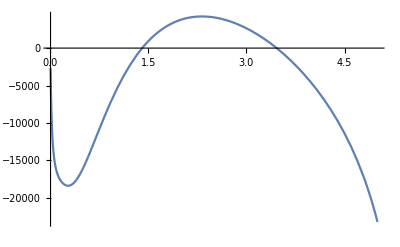

```mathematica
Plot[Barrier[0.01,T],{T,0.01,5}]
```

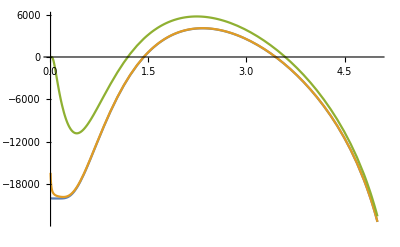

```mathematica
Plot[ {Barrier[0.00001,T], Barrier[0.001,T],Barrier[0.1,T]},{T,0.01,5}]
```

```mathematica
Plot[ {Barrier[0.00001,T], Barrier[0.001,T],Barrier[0.1,T]},{T,0.01,5}]
```

-Graphics-

g

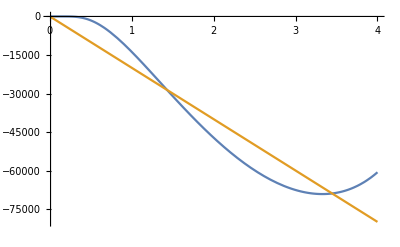

```mathematica
g
Plot[{Fsaddle[T],Fmetalow[0.001,T ]},{T,0.01,4}]
```

```mathematica
fava
```

{{1.54574×10^8,1.41421},{288023.,1.41421},{12435.6,1.41422},{1889.32,1.41426},{539.502,1.41441},{221.476,1.41478},{114.324,1.41547},{68.8573,1.41657},{46.2459,1.41815},{33.6339,1.42024},{25.9674,1.42283},{20.9871,1.42591},{17.5774,1.42946},{15.142,1.43343},{13.3412,1.43778},{11.9706,1.44248},{10.9019,1.44748},{10.0512,1.45275},{9.36208,1.45826}}

```mathematica
fava1 =Transpose@Append[Transpose@fava,T]
```

{{1.54574×10^8,1.41421,0.1},{288023.,1.41421,0.15},{12435.6,1.41422,0.2},{1889.32,1.41426,0.25},{539.502,1.41441,0.3},{221.476,1.41478,0.35},{114.324,1.41547,0.4},{68.8573,1.41657,0.45},{46.2459,1.41815,0.5},{33.6339,1.42024,0.55},{25.9674,1.42283,0.6},{20.9871,1.42591,0.65},{17.5774,1.42946,0.7},{15.142,1.43343,0.75},{13.3412,1.43778,0.8},{11.9706,1.44248,0.85},{10.9019,1.44748,0.9},{10.0512,1.45275,0.95},{9.36208,1.45826,1.}}

```mathematica
Apply[F1,fava1]
```

F1[{1.54574×10^8,1.41421,0.1},{288023.,1.41421,0.15},{12435.6,1.41422,0.2},{1889.32,1.41426,0.25},{539.502,1.41441,0.3},{221.476,1.41478,0.35},{114.324,1.41547,0.4},{68.8573,1.41657,0.45},{46.2459,1.41815,0.5},{33.6339,1.42024,0.55},{25.9674,1.42283,0.6},{20.9871,1.42591,0.65},{17.5774,1.42946,0.7},{15.142,1.43343,0.75},{13.3412,1.43778,0.8},{11.9706,1.44248,0.85},{10.9019,1.44748,0.9},{10.0512,1.45275,0.95},{9.36208,1.45826,1.}]

```mathematica
F1[3,2,8 ]
```

-400000/9

```mathematica
fava1[1,1,1]
```

{{1.54574×10^8,1.41421,0.1},{288023.,1.41421,0.15},{12435.6,1.41422,0.2},{1889.32,1.41426,0.25},{539.502,1.41441,0.3},{221.476,1.41478,0.35},{114.324,1.41547,0.4},{68.8573,1.41657,0.45},{46.2459,1.41815,0.5},{33.6339,1.42024,0.55},{25.9674,1.42283,0.6},{20.9871,1.42591,0.65},{17.5774,1.42946,0.7},{15.142,1.43343,0.75},{13.3412,1.43778,0.8},{11.9706,1.44248,0.85},{10.9019,1.44748,0.9},{10.0512,1.45275,0.95},{9.36208,1.45826,1.}}[1,1,1]

```mathematica
fava1[[1,1]]
```

1.54574×10^8

```mathematica
fava1
```

{{1.54574×10^8,1.41421,0.1},{288023.,1.41421,0.15},{12435.6,1.41422,0.2},{1889.32,1.41426,0.25},{539.502,1.41441,0.3},{221.476,1.41478,0.35},{114.324,1.41547,0.4},{68.8573,1.41657,0.45},{46.2459,1.41815,0.5},{33.6339,1.42024,0.55},{25.9674,1.42283,0.6},{20.9871,1.42591,0.65},{17.5774,1.42946,0.7},{15.142,1.43343,0.75},{13.3412,1.43778,0.8},{11.9706,1.44248,0.85},{10.9019,1.44748,0.9},{10.0512,1.45275,0.95},{9.36208,1.45826,1.}}

```mathematica
MatrixForm[fava1]
```

(1.54574×10^8 | 1.41421 | 0.1
288023. | 1.41421 | 0.15
12435.6 | 1.41422 | 0.2
1889.32 | 1.41426 | 0.25
539.502 | 1.41441 | 0.3
221.476 | 1.41478 | 0.35
114.324 | 1.41547 | 0.4
68.8573 | 1.41657 | 0.45
46.2459 | 1.41815 | 0.5
33.6339 | 1.42024 | 0.55
25.9674 | 1.42283 | 0.6
20.9871 | 1.42591 | 0.65
17.5774 | 1.42946 | 0.7
15.142 | 1.43343 | 0.75
13.3412 | 1.43778 | 0.8
11.9706 | 1.44248 | 0.85
10.9019 | 1.44748 | 0.9
10.0512 | 1.45275 | 0.95
9.36208 | 1.45826 | 1.)

```mathematica
c = {{1,3},{3,4}}
```

{{1,3},{3,4}}

```mathematica
fava2 = F1@@@fava1
```

{-0.0000129388,-0.0104159,-0.321694,-2.64844,-11.1506,-31.8093,-70.854,-133.45,-223.076,-341.47,-488.906,-664.581,-866.984,-1094.2,-1344.16,-1614.73,-1903.88,-2209.69,-2530.42}

```mathematica
Plot[{Fsaddle[T],Fmetalow[0.001,T ]},{T,0.01,4}]
```

-Graphics-

```mathematica
fava2
```

{-0.0000129388,-0.0104159,-0.321694,-2.64844,-11.1506,-31.8093,-70.854,-133.45,-223.076,-341.47,-488.906,-664.581,-866.984,-1094.2,-1344.16,-1614.73,-1903.88,-2209.69,-2530.42}

Transpose::tperm: Permutation {1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9} is longer than the dimensions {10} of the expression.

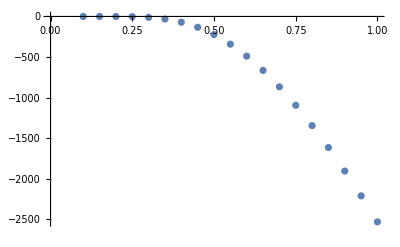

```mathematica
data = Transpose@{T, fava2};
numericsaddle = ListPlot[data]
```

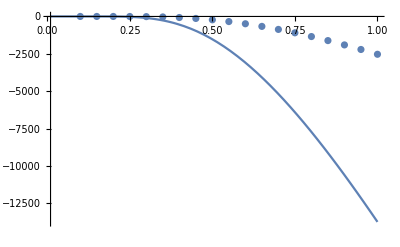

```mathematica
Show[Plot[Fsaddle[T],{T,0.01,1}], ListPlot[data],PlotRange->All]
```

```mathematica
Show[Plot[Fsaddle[T],{T,0.01,1}], ListPlot[data]]
```

-Graphics-

```mathematica
Barrier[ccrit_, T_]:= -(Fsaddle[T] - Fmetalow[ccrit, T])/T
```

```mathematica
Plot[Barrier[0.01,T],{T,0.01,5}]
```

-Graphics-

```mathematica
Show[Plot[Fsaddle[T],{T,0.01,1}], ListPlot[data]]
```

-Graphics-

```mathematica
FindRoot[{F1partx[x,0.2]==0,F1party[y,1]==0},{{x,Exp[saddleenergy/0.2]},{y,Sqrt[2]}}]
```

{x→12435.6,y→1.41424}

```mathematica
data = Transpose@{T, fava2};
```

```mathematica
metastable =  Transpose@{T, Transpose@ciro};

Show[ListPlot[metastable], ListPlot[data]]
```

Transpose::nmtx: The first two levels of {{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]} cannot be transposed.

ListPlot::lpn: Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}]],].

Show[ListPlot[Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}]],-Graphics-]

```mathematica
MatrixForm[fava2]
```

(-0.0000129388
-0.0104159
-0.321694
-2.64844
-11.1506
-31.8093
-70.854
-133.45
-223.076
-341.47
-488.906
-664.581
-866.984
-1094.2
-1344.16
-1614.73
-1903.88
-2209.69
-2530.42)

```mathematica
MatrixForm[ciro]
```

ciro

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
ListPlot[metastable]
```

ListPlot::lpn: Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}]]

```mathematica
data
```

{{0.1,-0.0000129388},{0.15,-0.0104159},{0.2,-0.321694},{0.25,-2.64844},{0.3,-11.1506},{0.35,-31.8093},{0.4,-70.854},{0.45,-133.45},{0.5,-223.076},{0.55,-341.47},{0.6,-488.906},{0.65,-664.581},{0.7,-866.984},{0.75,-1094.2},{0.8,-1344.16},{0.85,-1614.73},{0.9,-1903.88},{0.95,-2209.69},{1.,-2530.42}}

```mathematica
metastable
```

Transpose[{{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.},Transpose[ciro]}]